Below, the serial device is opened with the highest supported baud rate.
(TODO: Use .NET to surpass the 256,000 rate imposed by Mathematica)

```mathematica
S = DeviceOpen["Serial", {"COM8", "DataBits"->8,"Parity"->None,"StopBits" -> 1,"BaudRate"-> 256000}]
```

DeviceObject[…]

SingleSample requests the device to do one capture of the given amount of samples. This capture is done at the current sample rate.
A list of numbers of length ‘count’ is returned.

```mathematica
SingleSample[S_, count_]:=Module[{buf},
DeviceWrite[S, {114,BitAnd[count,255],BitAnd[BitShiftRight[count,8],255]}];
buf = DeviceReadList[S, count*2];
Table[(BitOr[buf[[i*2+1]],BitShiftLeft[buf[[i*2+2]],8]]), {i,0,count-1}]];
```

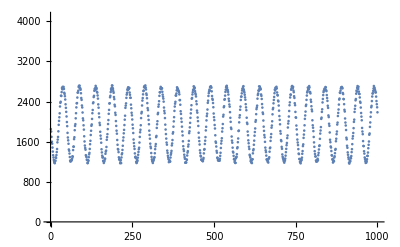

```mathematica
ListPlot[SingleSample[S,1000] , PlotRange->{0, 4096}]
```

```mathematica
DeviceClose[S];
```